# An Introduction to Mathematica

## Exercises

For the exam complete two of these... 

Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

```mathematica
f[x_]:= x*ⅇ^-x+ x*(1-x)
f@{0, 0.1, 0.2, 0.4}
```

{0,0.180484,0.323746,0.508128}

Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

```mathematica
BessJ1[x_] := BesselJ[1, x]
```

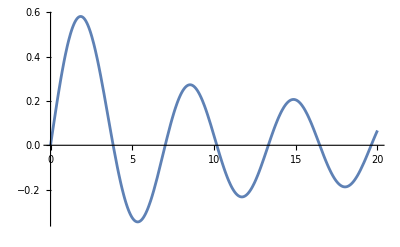

```mathematica
Plot[BessJ1[x], {x, 0, 20}]
```

```mathematica
FindRoot[BessJ1[x],{x,#}]&/@{4,7,10}
```

{{x→3.83171},{x→7.01559},{x→10.1735}}

Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

```mathematica
Integrate[Sin[x] ⅇ^-x, x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
D[%, x]
Simplify[%]
```

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

ⅇ^-x Sin[x]

Q4: Find the series expansion of the function f(x) = e^(-arctan(x)) about x=0, and about x → ∞. Hint: The arctan function is ArcTan[x].

```mathematica
f =Exp[-ArcTan[x]]
Series[f,{x,0,5}]
```

ⅇ^(-ArcTan[x])

1-x+x^2/2+x^3/6-(7 x^4)/24-x^5/24+O[x]^6

```mathematica
Series[f,{x,Infinity,5}]
```

ⅇ^(-π/2)+ⅇ^(-π/2)/x+ⅇ^(-π/2)/(2 x^2)-ⅇ^(-π/2)/(6 x^3)-(7 ⅇ^(-π/2))/(24 x^4)+ⅇ^(-π/2)/(24 x^5)+O[1/x]^6